# Partial Trace of a Multi-qubit System by Mark S. Tame School of Mathematics and Physics, Queen's University, Belfast. UK. m.tame@qub.ac.uk

## Introduction

For many situations in Quantum Information Theory it is necessary to trace out a subgroup of qubits from a larger group. For example, suppose Alice, Bob and Charlie each have a qubit with the total system described by the density matrix ρ_ABC. If we would like  to examine more closely the subsystem of qubits shared by just Alice and Bob we need to take the trace:
 ρ_AB=Tr_C{ρ_ABC }
However for large multi-qubit systems, calculating this by hand becomes quite unmanageable. What the TraceSystem  function does, is allow you to trace out an arbitrary number of qubits from a large system of N-qubits by getting Mathematica do the work for you:
TraceSystem[ρ_sys, {1,3,6,...}] = Tr_[1,3,6,...]{ρ_sys}
Where ρ_sys is in the computational basis eg. for 2 qubits we have:
Basis | <00| | <01| | <10| | <11|
|00> | a | b | c | d
|01> | e | f | g | h
|10> | i | j | k | l
|11> | m | n | o | p                            ρ_sys= (a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p)
To use the function, you must evaluate it first in The Code section. Then it is straightforward to use, see the Examples section for its possible uses.

## The Code

Here is the code for the TraceSystem  function to trace out an arbitrary number of qubits from an N-qubit quantum system. Evaluate the cell below and you can use it. For more help, please see the Examples section:

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
```

## Examples

Here are some examples of how it works. Just to remind you again, the density matrix must be in the computational basis eg. |0000...0><0000...0| corresponds to element ρ_00, with qubits numbered from 1 to N. TraceSystem has 2 arguments, the density matrix ρ and the list of qubits to trace out eg. {2, 3}. This list can be as long as you want and entered in any order, as it is reordered within the function anyway.
- Example 1.
In this example we have a three qubit system and we are tracing out the last qubit (qubit 3):

```mathematica
TraceSystem[({{a1, a2, a3, a4, a5, a6, a7, a8}, {b1, b2, b3, b4, b5, b6, b7, b8}, {c1, c2, c3, c4, c5, c6, c7, c8}, {d1, d2, d3, d4, d5, d6, d7, d8}, {e1, e2, e3, e4, e5, e6, e7, e8}, {f1, f2, f3, f4, f5, f6, f7, f8}, {g1, g2, g3, g4, g5, g6, g7, g8}, {h1, h2, h3, h4, h5, h6, h7, h8}}),{3}] //MatrixForm
```

(a1+b2 | a3+b4 | a5+b6 | a7+b8
c1+d2 | c3+d4 | c5+d6 | c7+d8
e1+f2 | e3+f4 | e5+f6 | e7+f8
g1+h2 | g3+h4 | g5+h6 | g7+h8)

This leaves us with the density matrix for qubits 1 and 2.

- Example 2.
In this example we have a three qubit system and we are tracing out qubits 2 and 3:

```mathematica
TraceSystem[({{a1, a2, a3, a4, a5, a6, a7, a8}, {b1, b2, b3, b4, b5, b6, b7, b8}, {c1, c2, c3, c4, c5, c6, c7, c8}, {d1, d2, d3, d4, d5, d6, d7, d8}, {e1, e2, e3, e4, e5, e6, e7, e8}, {f1, f2, f3, f4, f5, f6, f7, f8}, {g1, g2, g3, g4, g5, g6, g7, g8}, {h1, h2, h3, h4, h5, h6, h7, h8}}),{2,3}] //MatrixForm
```

(a1+b2+c3+d4 | a5+b6+c7+d8
e1+f2+g3+h4 | e5+f6+g7+h8)

Leaving us with the density matrix for qubit 1.

- Example 3.
In this example we have a four qubit system and we are tracing out qubits 1 and 4:

Leaving us with the density matrix for qubits 2 and 3.

## How does it Work?

```mathematica
SwapParts[expr_, pos1_, pos2_] := ReplacePart[#,#, {pos1,pos2}, {pos2,pos1}]&[expr]
TraceSystem[D_, s_]:= (

Qubits=Reverse[Sort[s]];
TrkM=D;

z=(Dimensions[Qubits][[1]]+1);

For[q=1,q<z,q++,
n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
 ],
For[j=0,j<(n-k),j++,
b={0};
For[i=1,i<2^n+1,i++,
If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1 && Count[b, i]  ==0, Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2, n]),{n},{n-j-1}],2]+1)}];

M=M[[perm,perm]];

 ]    
]         ;
TrkM={};
For[p=1,p<2^n+1,p=p+2,
TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];
]
   ];
]

]

;Return[TrkM])
Clear[t]
H0 = h{{0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,2,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,2,0,0},{0,0,0,0,0,0,2,0},{0,0,0,0,0,0,0,3}};
H = -{{0,0,0,0,0,0,0,0},{0,0,g,0,0,0,0,0},{0,g,0,0,g,0,0,0},{0,0,0,0,0,g,0,0},{0,0,g,0,0,0,0,0},{0,0,0,g,0,0,g,0},{0,0,0,0,0,g,0,0},{0,0,0,0,0,0,0,0}};
H12 = -{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
H0.H-H.H0;
U = MatrixExp[H I t]
UH2 = MatrixExp[H12 I t];
```

{{1,0,0,0,0,0,0,0},{0,1/2+1/2 Cos[√2 g t],-(ⅈ Sin[√2 g t])/(√2),0,-1/2+1/2 Cos[√2 g t],0,0,0},{0,-(ⅈ Sin[√2 g t])/(√2),Cos[√2 g t],0,-(ⅈ Sin[√2 g t])/(√2),0,0,0},{0,0,0,1/2+1/2 Cos[√2 g t],0,-(ⅈ Sin[√2 g t])/(√2),-1/2+1/2 Cos[√2 g t],0},{0,-1/2+1/2 Cos[√2 g t],-(ⅈ Sin[√2 g t])/(√2),0,1/2+1/2 Cos[√2 g t],0,0,0},{0,0,0,-(ⅈ Sin[√2 g t])/(√2),0,Cos[√2 g t],-(ⅈ Sin[√2 g t])/(√2),0},{0,0,0,-1/2+1/2 Cos[√2 g t],0,-(ⅈ Sin[√2 g t])/(√2),1/2+1/2 Cos[√2 g t],0},{0,0,0,0,0,0,0,1}}

```mathematica
MatrixForm[U]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2+1/2 Cos[√2 g t] | -(ⅈ Sin[√2 g t])/(√2) | 0 | -1/2+1/2 Cos[√2 g t] | 0 | 0 | 0
0 | -(ⅈ Sin[√2 g t])/(√2) | Cos[√2 g t] | 0 | -(ⅈ Sin[√2 g t])/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/2+1/2 Cos[√2 g t] | 0 | -(ⅈ Sin[√2 g t])/(√2) | -1/2+1/2 Cos[√2 g t] | 0
0 | -1/2+1/2 Cos[√2 g t] | -(ⅈ Sin[√2 g t])/(√2) | 0 | 1/2+1/2 Cos[√2 g t] | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ Sin[√2 g t])/(√2) | 0 | Cos[√2 g t] | -(ⅈ Sin[√2 g t])/(√2) | 0
0 | 0 | 0 | -1/2+1/2 Cos[√2 g t] | 0 | -(ⅈ Sin[√2 g t])/(√2) | 1/2+1/2 Cos[√2 g t] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
}120
```

```mathematica
Hthree = {{0,0,0,0,0,0,0,0},{0,3,0,0,0,0,0,0},{0,0,4,0,0,0,0,0},{0,0,0,7,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,4,0,0},{0,0,0,0,0,0,5,0},{0,0,0,0,0,0,0,8}};
Hfridge = {{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
Ufridge = MatrixExp[Hfridge I t];
```

```mathematica
MatrixForm[Ufridge];
```

```mathematica
H = -{{0,0,0,0,0,0,0,0},{0,0,g,0,0,0,0,0},{0,g,0,0,g,0,0,0},{0,0,0,0,0,g,0,0},{0,0,g,0,0,0,0,0},{0,0,0,g,0,0,g,0},{0,0,0,0,0,g,0,0},{0,0,0,0,0,0,0,0}};
U = MatrixExp[H I t];
UH2;
```

```mathematica
Ut = Transpose[{{1,0,0,0,0,0,0,0},{0,1/2+1/2 Cos[√2 g t],(ⅈ Sin[√2 g t])/(√2),0,-1/2+1/2 Cos[√2 g t],0,0,0},{0,(ⅈ Sin[√2 g t])/(√2),Cos[√2 g t],0,(ⅈ Sin[√2 g t])/(√2),0,0,0},{0,0,0,1/2+1/2 Cos[√2 g t],0,(ⅈ Sin[√2 g t])/(√2),-1/2+1/2 Cos[√2 g t],0},{0,-1/2+1/2 Cos[√2 g t],(ⅈ Sin[√2 g t])/(√2),0,1/2+1/2 Cos[√2 g t],0,0,0},{0,0,0,(ⅈ Sin[√2 g t])/(√2),0,Cos[√2 g t],(ⅈ Sin[√2 g t])/(√2),0},{0,0,0,-1/2+1/2 Cos[√2 g t],0,(ⅈ Sin[√2 g t])/(√2),1/2+1/2 Cos[√2 g t],0},{0,0,0,0,0,0,0,1}}];
UH2t = Transpose[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,Cos[t],0,ⅈ Sin[t],0,0,0},{0,0,0,1,0,0,0,0},{0,0,ⅈ Sin[t],0,Cos[t],0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}];
```

```mathematica
g1=1;
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1/2+1/2 Cos[√2 t],0,(ⅈ Sin[√2 t])/(√2),-1/2+1/2 Cos[√2 t],0},{0,0,ⅈ t,0,1,0,0,0},{0,0,0,(ⅈ Sin[√2 t])/(√2),0,Cos[√2 t],(ⅈ Sin[√2 t])/(√2),0},{0,0,0,-1/2+1/2 Cos[√2 t],0,(ⅈ Sin[√2 t])/(√2),1/2+1/2 Cos[√2 t],0},{0,0,0,0,0,0,0,1}}.UH2//FullSimplify;
```

```mathematica
g=1;

a1=0.14;
a2=0.16;
a3=0.3;
```

```mathematica
Clear[a1,a2, a3];
```

```mathematica
rho = KroneckerProduct[{{1-a1,0},{0,a1}}, {{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}];

Clear[a1,a2,a3]
rho = KroneckerProduct[{{1-a1,0},{0,a1}}, {{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}}];
```

```mathematica
Ut.U//FullSimplify
MatrixForm[rho]
```

{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,1}}

rho

```mathematica
rho1in = TraceSystem[rho , {2,3}];
rho2in = TraceSystem[rho , {1,3}];
rho3in = TraceSystem[rho , {1,2}];
```

```mathematica
Clear[t]
rhocohere = {{0.66825+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.12414588282690253+0. ⅈ,0.-0.04342352515488476 ⅈ,0.+0. ⅈ,0.08890898252523391+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0.04342352515488476 ⅈ,0.04493203494953215+0. ⅈ,0.+0. ⅈ,0.-0.0037222547530862994 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0055256634629883995+0. ⅈ,0.+0. ⅈ,0.-0.006468902419166835 ⅈ,-0.006219969970901138+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.08890898252523391+0. ⅈ,0.+0.003722254753086303 ⅈ,0.+0. ⅈ,0.1346720822235653+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0.006468902419166835 ⅈ,0.+0. ⅈ,0.013189939941802278+0. ⅈ,0.-0.00924635755015685 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.006219969970901139+0. ⅈ,0.+0. ⅈ,0.+0.00924635755015685 ⅈ,0.009034396595209321+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.00025+0. ⅈ}};
```

```mathematica
Uh2t.UH2//FullSimplify;
```

```mathematica
rhot = Ut.rho.U;
MatrixForm[rhot]
```

((1-a1) (1-a2) (1-a3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a1 (1-a2) (1-a3) (-1/2+1/2 Cos[√2 t])^2+(1-a1) (1-a2) a3 (1/2+1/2 Cos[√2 t])^2+1/2 (1-a1) a2 (1-a3) Sin[√2 t]^2 | -(ⅈ a1 (1-a2) (1-a3) (-1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)-(ⅈ (1-a1) (1-a2) a3 (1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)+(ⅈ (1-a1) a2 (1-a3) Cos[√2 t] Sin[√2 t])/(√2) | 0 | a1 (1-a2) (1-a3) (-1/2+1/2 Cos[√2 t]) (1/2+1/2 Cos[√2 t])+(1-a1) (1-a2) a3 (-1/2+1/2 Cos[√2 t]) (1/2+1/2 Cos[√2 t])+1/2 (1-a1) a2 (1-a3) Sin[√2 t]^2 | 0 | 0 | 0
0 | (ⅈ a1 (1-a2) (1-a3) (-1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)+(ⅈ (1-a1) (1-a2) a3 (1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)-(ⅈ (1-a1) a2 (1-a3) Cos[√2 t] Sin[√2 t])/(√2) | (1-a1) a2 (1-a3) Cos[√2 t]^2+1/2 a1 (1-a2) (1-a3) Sin[√2 t]^2+1/2 (1-a1) (1-a2) a3 Sin[√2 t]^2 | 0 | (ⅈ (1-a1) (1-a2) a3 (-1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)+(ⅈ a1 (1-a2) (1-a3) (1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)-(ⅈ (1-a1) a2 (1-a3) Cos[√2 t] Sin[√2 t])/(√2) | 0 | 0 | 0
0 | 0 | 0 | a1 a2 (1-a3) (-1/2+1/2 Cos[√2 t])^2+(1-a1) a2 a3 (1/2+1/2 Cos[√2 t])^2+1/2 a1 (1-a2) a3 Sin[√2 t]^2 | 0 | -(ⅈ a1 a2 (1-a3) (-1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)-(ⅈ (1-a1) a2 a3 (1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)+(ⅈ a1 (1-a2) a3 Cos[√2 t] Sin[√2 t])/(√2) | a1 a2 (1-a3) (-1/2+1/2 Cos[√2 t]) (1/2+1/2 Cos[√2 t])+(1-a1) a2 a3 (-1/2+1/2 Cos[√2 t]) (1/2+1/2 Cos[√2 t])+1/2 a1 (1-a2) a3 Sin[√2 t]^2 | 0
0 | a1 (1-a2) (1-a3) (-1/2+1/2 Cos[√2 t]) (1/2+1/2 Cos[√2 t])+(1-a1) (1-a2) a3 (-1/2+1/2 Cos[√2 t]) (1/2+1/2 Cos[√2 t])+1/2 (1-a1) a2 (1-a3) Sin[√2 t]^2 | -(ⅈ (1-a1) (1-a2) a3 (-1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)-(ⅈ a1 (1-a2) (1-a3) (1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)+(ⅈ (1-a1) a2 (1-a3) Cos[√2 t] Sin[√2 t])/(√2) | 0 | (1-a1) (1-a2) a3 (-1/2+1/2 Cos[√2 t])^2+a1 (1-a2) (1-a3) (1/2+1/2 Cos[√2 t])^2+1/2 (1-a1) a2 (1-a3) Sin[√2 t]^2 | 0 | 0 | 0
0 | 0 | 0 | (ⅈ a1 a2 (1-a3) (-1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)+(ⅈ (1-a1) a2 a3 (1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)-(ⅈ a1 (1-a2) a3 Cos[√2 t] Sin[√2 t])/(√2) | 0 | a1 (1-a2) a3 Cos[√2 t]^2+1/2 a1 a2 (1-a3) Sin[√2 t]^2+1/2 (1-a1) a2 a3 Sin[√2 t]^2 | (ⅈ (1-a1) a2 a3 (-1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)+(ⅈ a1 a2 (1-a3) (1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)-(ⅈ a1 (1-a2) a3 Cos[√2 t] Sin[√2 t])/(√2) | 0
0 | 0 | 0 | a1 a2 (1-a3) (-1/2+1/2 Cos[√2 t]) (1/2+1/2 Cos[√2 t])+(1-a1) a2 a3 (-1/2+1/2 Cos[√2 t]) (1/2+1/2 Cos[√2 t])+1/2 a1 (1-a2) a3 Sin[√2 t]^2 | 0 | -(ⅈ (1-a1) a2 a3 (-1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)-(ⅈ a1 a2 (1-a3) (1/2+1/2 Cos[√2 t]) Sin[√2 t])/(√2)+(ⅈ a1 (1-a2) a3 Cos[√2 t] Sin[√2 t])/(√2) | (1-a1) a2 a3 (-1/2+1/2 Cos[√2 t])^2+a1 a2 (1-a3) (1/2+1/2 Cos[√2 t])^2+1/2 a1 (1-a2) a3 Sin[√2 t]^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a1 a2 a3)

Take::take: Cannot take positions 2 through 2 in Symbol[].

```mathematica
rho1 = TraceSystem[rhot , {2,3}]//FullSimplify;
rho2 = TraceSystem[rhot , {1,3}]//FullSimplify;
rho3  = TraceSystem[rhot , {1,2}]//FullSimplify;
MatrixForm[rho1]
MatrixForm[rho2]
MatrixForm[rho3]
```

(1/8 (8-3 a1-2 a2-3 a3+4 (-a1+a3) Cos[√2 t]-(a1-2 a2+a3) Cos[2 √2 t]) | 0
0 | 1/8 (3 a1+2 a2+3 a3+4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t]))

(1/4 (4-a1-2 a2-a3+(a1-2 a2+a3) Cos[2 √2 t]) | 0
0 | 1/4 (a1+2 a2+a3-(a1-2 a2+a3) Cos[2 √2 t]))

(1/8 (8-3 a1-2 a2-3 a3+4 (a1-a3) Cos[√2 t]-(a1-2 a2+a3) Cos[2 √2 t]) | 0
0 | 1/8 (3 a1+2 a2+3 a3+4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t]))

```mathematica
Clear[a1,a2,a3]
rho12in = TraceSystem[rho , {3}]//FullSimplify;
rho13in = TraceSystem[rho , {2}]//FullSimplify;
rho23in = TraceSystem[rho, {1}]//FullSimplify;
rho12 = TraceSystem[rhot, {3}]//FullSimplify;
rho13 = TraceSystem[rhot , {2}]//FullSimplify;
rho23 = TraceSystem[rhot, {1}]//FullSimplify;
MatrixForm[rho13]
MatrixForm[rho12]
MatrixForm[rho23]
```

((-1+a1) (-1+a3) (1-a2+a2 Cos[√2 t]^2)+1/2 (-1+a2) (-a3+a1 (-1+2 a3)) Sin[√2 t]^2 | 0 | 0 | 0
0 | 1/8 (2 a2+a1 (3-2 a2-4 a3)+3 a3-2 a2 a3+4 (-a1+a3) Cos[√2 t]+(a1 (1+2 a2-4 a3)+2 a2 (-1+a3)+a3) Cos[2 √2 t]) | -1/4 (a1 (1+2 a2-4 a3)+2 a2 (-1+a3)+a3) Sin[√2 t]^2 | 0
0 | -1/4 (a1 (1+2 a2-4 a3)+2 a2 (-1+a3)+a3) Sin[√2 t]^2 | 1/8 (2 a2+a1 (3-2 a2-4 a3)+3 a3-2 a2 a3+4 (a1-a3) Cos[√2 t]+(a1 (1+2 a2-4 a3)+2 a2 (-1+a3)+a3) Cos[2 √2 t]) | 0
0 | 0 | 0 | 1/4 (a2 a3+a1 (a2+2 a3)-(a1 (a2-2 a3)+a2 a3) Cos[2 √2 t]))

((-1+a1) (-1+a2) a3 Cos[t/(√2)]^4+1/2 (-1+a3) (2 a1 (-1+a2) Sin[t/(√2)]^4+(-1+a1) (2-2 a2+a2 Sin[√2 t]^2)) | 0 | 0 | 0
0 | 1/8 (4 a2+a1 (2-3 a2-2 a3)+2 a3-3 a2 a3+4 a2 (-a1+a3) Cos[√2 t]-(-4 a2+a1 (2+a2-2 a3)+(2+a2) a3) Cos[2 √2 t]) | (ⅈ (a1-a3+(a1-2 a2+a3) Cos[√2 t]) Sin[√2 t])/(2 √2) | 0
0 | -(ⅈ (a1-a3+(a1-2 a2+a3) Cos[√2 t]) Sin[√2 t])/(2 √2) | 1/8 (2 a2+a1 (3-3 a2-2 a3)+3 a3-3 a2 a3-4 (-1+a2) (a1-a3) Cos[√2 t]+(a3-a2 (2+a3)+a1 (1-a2+2 a3)) Cos[2 √2 t]) | 0
0 | 0 | 0 | 1/8 (3 a1 a2+2 a1 a3+3 a2 a3+4 a2 (a1-a3) Cos[√2 t]+(a1 a2-2 a1 a3+a2 a3) Cos[2 √2 t]))

(a1 (-1+a2) (-1+a3) Cos[t/(√2)]^4+1/2 (-1+a1) (2 (-1+a2) a3 Sin[t/(√2)]^4+(-1+a3) (2-2 a2+a2 Sin[√2 t]^2)) | 0 | 0 | 0
0 | 1/8 (2 a2+a1 (3-3 a2-2 a3)+3 a3-3 a2 a3+4 (-1+a2) (a1-a3) Cos[√2 t]+(a3-a2 (2+a3)+a1 (1-a2+2 a3)) Cos[2 √2 t]) | -(ⅈ (-a1+a3+(a1-2 a2+a3) Cos[√2 t]) Sin[√2 t])/(2 √2) | 0
0 | (ⅈ (-a1+a3+(a1-2 a2+a3) Cos[√2 t]) Sin[√2 t])/(2 √2) | 1/8 (4 a2+a1 (2-3 a2-2 a3)+2 a3-3 a2 a3+4 a2 (a1-a3) Cos[√2 t]-(-4 a2+a1 (2+a2-2 a3)+(2+a2) a3) Cos[2 √2 t]) | 0
0 | 0 | 0 | 1/8 (3 a1 a2+2 a1 a3+3 a2 a3+4 a2 (-a1+a3) Cos[√2 t]+(a1 a2-2 a1 a3+a2 a3) Cos[2 √2 t]))

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Take::take: Cannot take positions 2 through 2 in Symbol[].

```mathematica
Hint3= TraceSystem[H , {2,1}];
Hint23 = TraceSystem[H,{1}];
Hint13 = TraceSystem[H , {2}];
Com = Hint12.{{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,2}} - {{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,2}}.Hint12;
```

```mathematica
Eint12in = Tr[rhocohere12.Hint12];
H1 = TraceSystem[H0, {2,3}];
Htrace2 =TraceSystem[H0, {1,3}] ;
H3 = TraceSystem[H0, {1,2}];
Eint1t = Tr[rho1.H1];
Eint2t = Tr[rho2.Htrace2];
Eint3t = Tr[rho3.H3];
Eint23in = Tr[rho23in.Hint23];
Eint23t = Tr[rho23.Hint23];
Eint13in = Tr[rho13in.Hint13];
Eint13t = Tr[rho13.Hint13];
```

```mathematica
S12in = -Tr[rho12in.MatrixLog[rho12in]];
S12t = -Tr[rho12.MatrixLog[rho12]];
S13in = -Tr[rho13in.MatrixLog[rho13in]];
S13t = -Tr[rho13.MatrixLog[rho13]];
S23in = -Tr[rho23in.MatrixLog[rho23in]];
S23t = -Tr[rho23.MatrixLog[rho23]];
```

```mathematica
g1=1;
```

```mathematica
S1= -Tr[rho1.MatrixLog[rho1]]
S1in = -Tr[rho1in.MatrixLog[rho1in]]
```

-1/8 (8-3 a1-2 a2-3 a3+4 (-a1+a3) Cos[√2 t]-(a1-2 a2+a3) Cos[2 √2 t]) Log[1/8 (8-3 a1-2 a2-3 a3-4 (a1-a3) Cos[√2 t]-(a1-2 a2+a3) Cos[2 √2 t])]-1/8 (3 a1+2 a2+3 a3+4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t]) Log[1/8 (3 a1+2 a2+3 a3+4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t])]

-((1-a1) (1-a2) (1-a3)+(1-a1) a2 (1-a3)+(1-a1) (1-a2) a3+(1-a1) a2 a3) Log[1-a1]-(a1 (1-a2) (1-a3)+a1 a2 (1-a3)+a1 (1-a2) a3+a1 a2 a3) Log[a1]

```mathematica
Plot[{Tr[rho1.rho1],Tr[rho2.rho2],Tr[rho3.rho3],Tr[rho1.rho1]+Tr[rho2.rho2]+Tr[rho3.rho3],Tr[rhot.rhot]},{t,0,8}]
```

-Graphics-

```mathematica
S2= -Tr[rho2.MatrixLog[rho2]]//Simplify
S2in= -Tr[rho2in.MatrixLog[rho2in]]//Simplify
```

-1/4 (a1+2 a2+a3-(a1-2 a2+a3) Cos[2 √2 t]) Log[1/4 (a1+2 a2+a3-(a1-2 a2+a3) Cos[2 √2 t])]-1/4 (4-a1-2 a2-a3+(a1-2 a2+a3) Cos[2 √2 t]) Log[1/4 (4-a1-2 a2-a3+(a1-2 a2+a3) Cos[2 √2 t])]

(-1+a2) Log[1-a2]-a2 Log[a2]

```mathematica
S3= -Tr[rho3.MatrixLog[rho3]]//Simplify
S3in= -Tr[rho3in.MatrixLog[rho3in]]//Simplify
```

1/8 ((-8+3 a1+2 a2+3 a3-4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t]) Log[1/8 (8-3 a1-2 a2-3 a3+4 (a1-a3) Cos[√2 t]-(a1-2 a2+a3) Cos[2 √2 t])]-(3 a1+2 a2+3 a3+4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t]) Log[1/8 (3 a1+2 a2+3 a3-4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t])])

(-1+a3) Log[1-a3]-a3 Log[a3]

```mathematica
S1 +S2+S3//FullSimplify;
S1-S2//FullSimplify;
S1-S3//FullSimplify;
S2-S3//FullSimplify;
```

```mathematica
S123 = -Tr[rho.MatrixLog[rho]];
Subad1= S123 - S13t-S12t +S1;
Subad2 = S123 - S23t-S12t +S2;
Subad3= S123 - S13t-S23t +S3;
Rasterize[Plot[{S1,S2 , S3, S1+S2+S3, Subad1 , Subad2, Subad3} ,{t,0,8}, Background->White ,PlotLegends->"Expressions"]];
Rasterize[Plot[{S1,S2 , S3, S1+S2+S3, Abs[S1-S2]+Abs[S2-S3] +Abs[S1-S3]} ,{t,0,8}, Background->White ,PlotLegends->"Expressions"]];
Plot[{S1,S2 , S3, S12t} , Background->White ,PlotLegends->"Expressions",{t,0,8}]
Rasterize[Plot[{S1+S2+S3,Abs[S1-S2]+Abs[S2-S3] +Abs[S1-S3]},{t,0,8},Background->White ,PlotLegends->"Expressions"]];
Rasterize[Plot[{-S12t - S3 + (S1 +S2+S3), -S13t - S2 + (S1 +S2+S3), -S23t - S1 + (S1 +S2+S3)} ,{t,0,8},Background->White ,PlotLegends->"Expressions"]];
Rasterize[Plot[{S23t,S12t,S13t} ,{t,0,8},Background->White ,PlotLegends->"Expressions"]];
```

Plot[{S1,S2,S3,S12t},Background→White,PlotLegends→Expressions,{t,0,8}]

```mathematica
a1=0.3;
a2=0.2;
a3=0.2;
```

```mathematica
Clear[a1,a2,a3,rho1pop]
```

```mathematica
rho1pop[a1_,a2_,a3_,t_]:= rho1[[2,2]]
rho1pop[0.1,0.3,0.2,t]
```

1/8 (3 a1+2 a2+3 a3+4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t])

```mathematica
Manipulate[Plot[1/8 (3 a1+2 a2+3 a3+4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t]),{t,-8,8}],{a1,0,0.5},{a2,0,0.5},{a3,0,0.5}]
```

```mathematica
Plot[{S1+S2-S12t,S123-( S1+S2+S3 ), Abs[S1-S2]+Abs[S2-S3] +Abs[S1-S3],2Abs[Srholo1-Srholo2]}, {t,0,8},Background->White,PlotLegends->"Expressions"];
Plot[{Det[rho1],Det[rho2],Det[rho3],Det[rholo1],Det[rholo2]}, {t,0,8},Background->White,PlotLegends->"Expressions"];
```

0.229444

0.107173

0.374227

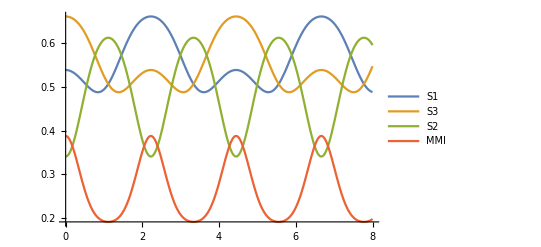

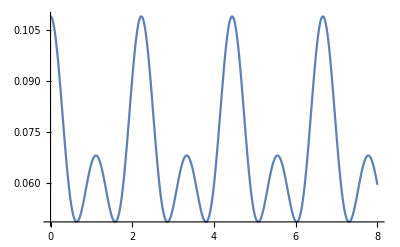

```mathematica
S=-Tr[rho.MatrixLog[rho]];
MMI=S12t+S13t+S23t-S1-S2-S3-S;
a1=RandomReal[{0,0.5}]
a2=RandomReal[{0,0.5}]
a3=RandomReal[{0,0.5}]
Plot[{S1,S3,S2,MMI}, {t,0,8},Background->White,PlotLegends->"Expressions"]
Plot[{S12t+S13t+S23t-S1-S2-S3-S}, {t,0,8},Background->White,PlotLegends->"Expressions"]
```

```mathematica
Rasterize[Plot[{S1+S3-(S1in + S2in),S1+S3 -(S2in + S3in ), S1+S3-( S1in + S3in)},{t, 0,8}, Background->White ,PlotLegends->"Expressions"]];
Rasterize[Plot[{S1+S2-(S1in + S3in),S1+S2 -(S2in + S3in ), S1+S2-( S1in + S2in)},{t, 0,8}, Background->White ,PlotLegends->"Expressions"]];
Rasterize[Plot[{S2+S3-(S1in + S2in),S2+S3 -(S2in + S3in ), S2+S3-( S1in + S3in)},{t, 0,8}, Background->White ,PlotLegends->"Expressions"]];
For the third qubit the final entropy is lower than what it started with.Is this a sign of non markovian or just a sign of the 3 qubit interaction. lowering of env is rising of system 
This maxima condition tells me what is the free energy I can extract
```

3 a^2 entropy env final For is^2 it just lower markovian non of^4 or qubit^2 rising sign^2 started system than the^3 third this what interaction.lowering with.Is

ⅈ can condition energy extract free is maxima me tells the This what

```mathematica
Rasterize[Plot[{ S1+S2+S3, Abs[S1-S2]+Abs[S2-S3] +Abs[S1-S3]},{t,0,8},Background->White ,PlotLegends->"Expressions"]];
```

```mathematica
FreeE1 = Tr[rho1.{{0,0},{0,h}}]-S1 -(Tr[rho1in.{{0,0},{0,h}}] - S1in);
```

```mathematica
FreeE2 = Tr[rho2.{{0,0},{0,h}}]-S2 -(Tr[rho2in.{{0,0},{0,h}}] - S2in);
```

```mathematica
FreeE3 = Tr[rho3.{{0,0},{0,h}}]-S3 -(Tr[rho3in.{{0,0},{0,h}}] - S3in);
```

```mathematica
Simplify[FreeE3]
```

1/8 (-8 a3 h+h (3 a1+2 a2+3 a3+4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t])+8 (-1+a3) Log[1-a3]-8 a3 Log[a3]-(-8+3 a1+2 a2+3 a3-4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t]) Log[1/8 (8-3 a1-2 a2-3 a3+4 (a1-a3) Cos[√2 t]-(a1-2 a2+a3) Cos[2 √2 t])]+(3 a1+2 a2+3 a3+4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t]) Log[1/8 (3 a1+2 a2+3 a3-4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t])])

```mathematica
Rasterize[ Plot[{FreeE1+FreeE2+FreeE3, FreeE1,FreeE2,FreeE3},{t,0,6 π}, Background->White ,PlotLegends->"Expressions"]]
```

-Graphics-

```mathematica
Ein = Tr[rho.H0];
Efi = Tr[rhot.H0]//FullSimplify;
Eint = -g1 Tr[rho.H]//FullSimplify;
Eintf = -g1 Tr[rhot.H]//FullSimplify;
Efis = Tr[rho1.{{0,0},{0,h}}]+Tr[rho2.{{0,0},{0,h}}]+Tr[rho3.{{0,0},{0,h}}]//FullSimplify;
```

```mathematica
h=1
```

1

```mathematica
S13 = Tr[rho13.MatrixLog[rho13]]//Simplify;
```

```mathematica
rhob = KroneckerProduct[{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}},{{1-c1,0},{0,c1}}]
{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}};
rhob1in = TraceSystem[rhob , {2,3}];
rhob2in = TraceSystem[rhob , {1,3}];
rhob3in = TraceSystem[rhob , {1,2}];
rhob12in = TraceSystem[rhob , {3}];
rhob13in = TraceSystem[rhob , {2}];
rhob23in = TraceSystem[rhob , {1}];
rhobt = U.rhob.Ut;
rhob1 = TraceSystem[rhobt , {2,3}];
rhob2 = TraceSystem[rhobt , {1,3}];
rhob3 = TraceSystem[rhobt , {1,2}];
rhob12 = TraceSystem[rhobt , {3}];
rhob13 = TraceSystem[rhobt , {2}];
rhob23 = TraceSystem[rhobt , {1}];
Tr[rhob1]//Simplify;
Tr[rhob2]//Simplify;
Tr[rhob3]//Simplify;
Tr[rhob12]//Simplify;
Tr[rhob13]//Simplify;
Tr[rhob23]//Simplify;
Tr[rhob.H0];
Tr[rhobt.H0];
Efisb = Tr[rhob1.{{0,0},{0,h}}]+Tr[rhob2.{{0,0},{0,h}}]+Tr[rhob3.{{0,0},{0,h}}]//FullSimplify;
Tr[rhob1.{{0,0},{0,h}}] //Simplify;
Tr[rhob1in.{{0,0},{0,h}}];
Tr[rhob2.{{0,0},{0,h}}] //Simplify;
Tr[rhob2in.{{0,0},{0,h}}];
Tr[rhob3.{{0,0},{0,h}}] //Simplify;
Tr[rhob3in.{{0,0},{0,h}}];
S12= -Tr[rhob12. MatrixLog[rhob12]];
S13= -Tr[rhob13. MatrixLog[rhob13]];
```

{{(1-c1)/2,0,0,0,0,0,(1-c1)/2,0},{0,c1/2,0,0,0,0,0,c1/2},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{(1-c1)/2,0,0,0,0,0,(1-c1)/2,0},{0,c1/2,0,0,0,0,0,c1/2}}

```mathematica
MatrixForm[{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}];
```

```mathematica
Sb1 = -Tr[rhob1.MatrixLog[rhob1]];
Sb1in = -Tr[rhob1in.MatrixLog[rhob1in]];
Sb2 = -Tr[rhob2.MatrixLog[rhob2]];
Sb2in = -Tr[rhob2in.MatrixLog[rhob2in]];
Sb3 = -Tr[rhob3.MatrixLog[rhob3]];
Sb3in = -Tr[rhob3in.MatrixLog[rhob3in]];
Sbdiff12 =S12tb - S12inb;

c1=0.4
```

0.4

```mathematica
Rasterize[Plot[{Sb1+Sb2-S12},{t,0,8}, Background->White ,PlotLegends->"Expressions"] ];
```

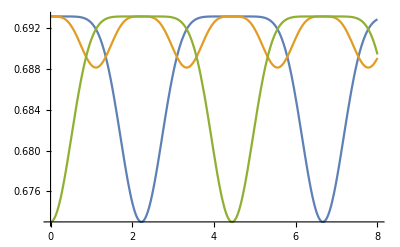

```mathematica
Plot[{Sb1, Sb2 , Sb3, S12tb},{t,0,8}]
How much A gets entangled depends on the initial of the C qubit. Since the B will continue entangling until it is fully entangled. Can we say something about the time taken to completely entangle? ;
```

```mathematica
Plot[Sb2+Sb1-S12,{t,0,100}];
```

```mathematica
Plot[Sb3 , {t,0,8}];
```

```mathematica
h=1
Freenet = FreeEb1 +FreeEb2+FreeEb3;
FreeEb1 = Tr[rhob1.{{0,0},{0,h}}] - Sb1 - (Tr[rhob1in.{{0,0},{0,h}}] - Sb1in);
FreeEb2 = Tr[rhob2.{{0,0},{0,h}}] - Sb2 - (Tr[rhob2in.{{0,0},{0,h}}] - Sb2in);
FreeEb3 = Tr[rhob3.{{0,0},{0,h}}] - Sb3 - (Tr[rhob3in.{{0,0},{0,h}}] - Sb3in);
```

1

```mathematica
Clear[t,a1,a2,a3]
MatrixForm[rho13]
Pauliy = KroneckerProduct[PauliMatrix[2],PauliMatrix[2]];
R = Pauliy*rho13*Pauliy;
Eigenvalues[R]
Eig13 = Abs[rho13[[2,3]]]-(rho13[[1,1]]*rho13[[4,4]])^0.5;
Eig12 = Abs[rho12[[2,3]]]-(rho12[[1,1]]*rho12[[4,4]])^0.5;
Eig23 = Abs[rho23[[2,3]]]-(rho23[[1,1]]*rho23[[4,4]])^0.5;
```

((-1+a1) (-1+a3) (1-a2+a2 Cos[√2 t]^2)+1/2 (-1+a2) (-a3+a1 (-1+2 a3)) Sin[√2 t]^2 | 0 | 0 | 0
0 | 1/8 (2 a2+a1 (3-2 a2-4 a3)+3 a3-2 a2 a3+4 (-a1+a3) Cos[√2 t]+(a1 (1+2 a2-4 a3)+2 a2 (-1+a3)+a3) Cos[2 √2 t]) | -1/4 (a1 (1+2 a2-4 a3)+2 a2 (-1+a3)+a3) Sin[√2 t]^2 | 0
0 | -1/4 (a1 (1+2 a2-4 a3)+2 a2 (-1+a3)+a3) Sin[√2 t]^2 | 1/8 (2 a2+a1 (3-2 a2-4 a3)+3 a3-2 a2 a3+4 (a1-a3) Cos[√2 t]+(a1 (1+2 a2-4 a3)+2 a2 (-1+a3)+a3) Cos[2 √2 t]) | 0
0 | 0 | 0 | 1/4 (a2 a3+a1 (a2+2 a3)-(a1 (a2-2 a3)+a2 a3) Cos[2 √2 t]))

{-1/4 (a1-2 a2+2 a1 a2+a3-4 a1 a3+2 a2 a3) Sin[√2 t]^2,1/4 (a1-2 a2+2 a1 a2+a3-4 a1 a3+2 a2 a3) Sin[√2 t]^2,0,0}

```mathematica
t=π/(2(2)^0.5)
DensityPlot3D[Eig13,{a1,0,0.5},{a2,0,0.5},{a3,0,0.5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,Automatic}]
DensityPlot3D[Eig12,{a1,0,0.5},{a2,0,0.5},{a3,0,0.5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,Automatic}]
DensityPlot3D[Eig23,{a1,0,0.5},{a2,0,0.5},{a3,0,0.5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,Automatic}]
```

1.11072

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
g=1;
Clear[a1,a2]
Clear[T];
Hfreefor2 = {{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,2}};
Hfor2= {{0,0,0,0},{0,0,ⅈ g,0},{0,-ⅈ g,0,0},{0,0,0,0}};
Ufor2 =  {{1,0,0,0},{0,Cos[T],-Exp[-ⅈ G]Sin[T],0},{0,Exp[ⅈ G]Sin[T],Cos[T],0},{0,0,0,1}};
rhofor2 = KroneckerProduct[{{1-a1,0},{0,a1}}, {{1-a2,0},{0,a2}}];
Ufor2t = Transpose[{{1,0,0,0},{0,Cos[T],-Exp[ⅈ G]Sin[T],0},{0,Exp[-ⅈ G]Sin[T],Cos[T],0},{0,0,0,1}}];
Ufor2.Ufor2t//FullSimplify;
rhofor2t = Ufor2.rhofor2.Ufor2t//FullSimplify
Eigfor2= Abs[rhofor2t[[2,3]]]-(rhofor2t[[1,1]]*rhofor2t[[4,4]])^0.5;
p1 = TraceSystem[rhofor2t,{2}]//FullSimplify  ;
p2 = TraceSystem[rhofor2t,{1}]//FullSimplify ;
p1in = TraceSystem[rhofor2,{2}]//FullSimplify  ;
p2in = TraceSystem[rhofor2,{1}]//FullSimplify ;
Abs[p1[[2,2]]-p2[[2,2]] ]//FullSimplify
rhofor2bathqubit = TraceSystem[rhofor2,{1}]
Enother = -Tr[rhofor2bathqubit .MatrixLog[rhofor2bathqubit]]
```

{{(-1+a1) (-1+a2),0,0,0},{0,-(-1+a1) a2 Cos[T]^2-a1 (-1+a2) Sin[T]^2,(-a1+a2) ⅇ^(-ⅈ G) Cos[T] Sin[T],0},{0,-(a1-a2) ⅇ^(ⅈ G) Cos[T] Sin[T],-a1 (-1+a2) Cos[T]^2-(-1+a1) a2 Sin[T]^2,0},{0,0,0,a1 a2}}

Abs[(a1-a2) Cos[2 T]]

{{(1-a1) (1-a2)+a1 (1-a2),0},{0,(1-a1) a2+a1 a2}}

-((1-a1) (1-a2)+a1 (1-a2)) Log[1-a2]-((1-a1) a2+a1 a2) Log[a2]

```mathematica
p2[[2,2]];
a1=0.45
a2=0.05
T=2
```

0.45

0.05

2

```mathematica
Clear[a1,a2,T]
a2 = En-a1
```

```mathematica
ExtracWork = p2[[2,2]]/Log[(1-p2[[2,2]])/p2[[2,2]]](Tr[p1.MatrixLog[p1]]-Tr[p1.MatrixLog[p2]])-p2in[[2,2]]/Log[(1-p2in[[2,2]])/p2in[[2,2]]](Tr[p1in.MatrixLog[p1in]]-Tr[p1in.MatrixLog[p2in]])//FullSimplify
```

0.122745

```mathematica
cde3
```

```mathematica
En=0.5
Plot3D[ExtracWork,{T,0,2.2214414690791826},{a1,0,0.5}]
```

0.5

-Graphics3D-

```mathematica
Simplify[ExtracWork]
```

(a2 ((-1+a1) Log[1-a1]-a1 Log[a1]+Log[1-a2]-a1 Log[1-a2]+a1 Log[a2]))/Log[-1+1/a2]+1/(4 Log[-(-2+a1+a2+(-a1+a2) Cos[2 T])/(a1+a2+(-a1+a2) Cos[2 T])])(a1+a2+(-a1+a2) Cos[2 T]) ((-2+a1+a2+(a1-a2) Cos[2 T]) Log[1/2 (2-a1-a2+(a1-a2) Cos[2 T])]+(a1+a2+(a1-a2) Cos[2 T]) Log[1/2 (a1+a2+(a1-a2) Cos[2 T])]-(-2+a1+a2+(a1-a2) Cos[2 T]) Log[1/2 (2-a1-a2+(-a1+a2) Cos[2 T])]-(a1+a2+(a1-a2) Cos[2 T]) Log[1/2 (a1+a2+(-a1+a2) Cos[2 T])])

```mathematica
cd\0e3
```

```mathematica
\00e3
```

```mathematica
T = π/4
```

π/4

```mathematica
Clear[T,a1,a2] 
rhofor20 = KroneckerProduct[{{1-a1,0},{0,a1}}, {{1-a2,0},{0,a2}}];
rhofor2t1 = Ufor2.rhofor20.Ufor2t//FullSimplify;
rhofor2t11 =TraceSystem[rhofor2t1,{2}]//FullSimplify  
En1 = -Tr[rhofor2t11 .MatrixLog[rhofor2t11 ]] ;

rhofor21 = KroneckerProduct[rhofor2t11, {{1-a2,0},{0,a2}}];
rhofor2t2 = Ufor2.rhofor21.Ufor2t//FullSimplify;
rhofor2t12 =TraceSystem[rhofor2t2,{2}]//FullSimplify   
En2 = -Tr[rhofor2t12 .MatrixLog[rhofor2t12 ]] ;

rhofor22 = KroneckerProduct[rhofor2t12, {{1-a2,0},{0,a2}}];
rhofor2t3 = Ufor2.rhofor22.Ufor2t//FullSimplify;
rhofor2t13 =TraceSystem[rhofor2t3,{2}]//FullSimplify   
En3 = -Tr[rhofor2t13 .MatrixLog[rhofor2t13]] ;

rhofor23 = KroneckerProduct[rhofor2t13, {{1-a2,0},{0,a2}}];
rhofor2t4 = Ufor2.rhofor23.Ufor2t//FullSimplify;
rhofor2t14 =TraceSystem[rhofor2t4,{2}]//FullSimplify   
En4 = -Tr[rhofor2t14 .MatrixLog[rhofor2t14 ]] ;

rhofor24 = KroneckerProduct[rhofor2t14, {{1-a2,0},{0,a2}}];
rhofor2t5 = Ufor2.rhofor24.Ufor2t//FullSimplify;
rhofor2t15 =TraceSystem[rhofor2t5,{2}]//FullSimplify   
En5 = -Tr[rhofor2t15 .MatrixLog[rhofor2t15]] ;

rhofor25 = KroneckerProduct[rhofor2t15, {{1-a2,0},{0,a2}}];
rhofor2t6 = Ufor2.rhofor25.Ufor2t//FullSimplify;
rhofor2t16 =TraceSystem[rhofor2t6,{2}]//FullSimplify   
En6 = -Tr[rhofor2t16 .MatrixLog[rhofor2t16]];

rhofor26 = KroneckerProduct[rhofor2t16, {{1-a2,0},{0,a2}}];
rhofor2t7 = Ufor2.rhofor26.Ufor2t//FullSimplify;
rhofor2t17 =TraceSystem[rhofor2t7,{2}]//FullSimplify   
En7 = -Tr[rhofor2t17 .MatrixLog[rhofor2t17]];
```

{{1/2 (2-a1-a2+(-a1+a2) Cos[2 T]),0},{0,1/2 (a1+a2+(a1-a2) Cos[2 T])}}

{{1/8 (8-3 a1-5 a2-(a1-a2) (4 Cos[2 T]+Cos[4 T])),0},{0,1/8 (3 a1+5 a2+(a1-a2) (4 Cos[2 T]+Cos[4 T]))}}

{{1/32 (32-10 a1-22 a2-(a1-a2) (15 Cos[2 T]+6 Cos[4 T]+Cos[6 T])),0},{0,1/32 (10 a1+22 a2+(a1-a2) (15 Cos[2 T]+6 Cos[4 T]+Cos[6 T]))}}

{{1/128 (128-35 a1-93 a2-(a1-a2) (56 Cos[2 T]+28 Cos[4 T]+8 Cos[6 T]+Cos[8 T])),0},{0,1/128 (35 a1+93 a2+(a1-a2) (56 Cos[2 T]+28 Cos[4 T]+8 Cos[6 T]+Cos[8 T]))}}

{{1/512 (512-126 a1-386 a2-(a1-a2) (5 (42 Cos[2 T]+24 Cos[4 T]+9 Cos[6 T]+2 Cos[8 T])+Cos[10 T])),0},{0,1/512 (126 a1+386 a2+(a1-a2) (5 (42 Cos[2 T]+24 Cos[4 T]+9 Cos[6 T]+2 Cos[8 T])+Cos[10 T]))}}

{{(2048-462 a1-1586 a2-(a1-a2) (792 Cos[2 T]+495 Cos[4 T]+220 Cos[6 T]+66 Cos[8 T]+12 Cos[10 T]+Cos[12 T]))/2048,0},{0,(462 a1+1586 a2+(a1-a2) (792 Cos[2 T]+495 Cos[4 T]+220 Cos[6 T]+66 Cos[8 T]+12 Cos[10 T]+Cos[12 T]))/2048}}

{{(8192-1716 a1-6476 a2-(a1-a2) (91 (33 Cos[2 T]+22 Cos[4 T]+11 Cos[6 T]+4 Cos[8 T]+Cos[10 T])+14 Cos[12 T]+Cos[14 T]))/8192,0},{0,(1716 a1+6476 a2+(a1-a2) (91 (33 Cos[2 T]+22 Cos[4 T]+11 Cos[6 T]+4 Cos[8 T]+Cos[10 T])+14 Cos[12 T]+Cos[14 T]))/8192}}

0.45

0.3

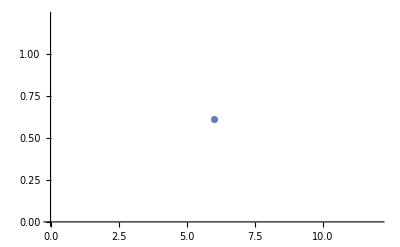

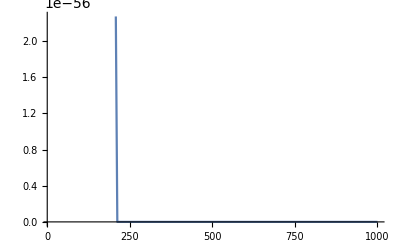

```mathematica
a1=0.45
a2=0.3
ListPlot[{{1,En1},{2,En2},{3,En3},{4,En4},{5,En5},{6,Enother}}]
Plot[2x/2^x,{x,10,1000}]
```

```mathematica
RR:=RandomReal[NormalDistribution[0,1]];RC:=RR+I*RR;
RG[n_]:=Table[RC,{n},{n}];RU[n_]:=Orthogonalize[RG[n]];
UnitaryMatrixQ[RU[4]]
```

True

```mathematica
unitary = RU[4] 
transposeunitary = ConjugateTranspose[unitary]
unitary.transposeunitary//FullSimplify
```

{{0.39413-0.00337169 ⅈ,-0.277821+0.361463 ⅈ,-0.284571-0.375592 ⅈ,-0.491829+0.41577 ⅈ},{0.326239-0.320213 ⅈ,-0.232436+0.482967 ⅈ,-0.0138063-0.140155 ⅈ,0.363512-0.593105 ⅈ},{-0.277022+0.684775 ⅈ,0.0572523+0.647164 ⅈ,0.0155029+0.160735 ⅈ,0.0781207-0.00799433 ⅈ},{-0.144058-0.263194 ⅈ,0.119726+0.261615 ⅈ,0.79983-0.303829 ⅈ,0.0389346+0.306012 ⅈ}}

{{0.39413+0.00337169 ⅈ,0.326239+0.320213 ⅈ,-0.277022-0.684775 ⅈ,-0.144058+0.263194 ⅈ},{-0.277821-0.361463 ⅈ,-0.232436-0.482967 ⅈ,0.0572523-0.647164 ⅈ,0.119726-0.261615 ⅈ},{-0.284571+0.375592 ⅈ,-0.0138063+0.140155 ⅈ,0.0155029-0.160735 ⅈ,0.79983+0.303829 ⅈ},{-0.491829-0.41577 ⅈ,0.363512+0.593105 ⅈ,0.0781207+0.00799433 ⅈ,0.0389346-0.306012 ⅈ}}

{{1.+0. ⅈ,-5.55112×10^-17+2.77556×10^-17 ⅈ,4.16334×10^-17+2.08167×10^-17 ⅈ,0.+0. ⅈ},{-5.55112×10^-17-2.77556×10^-17 ⅈ,1.+0. ⅈ,4.85723×10^-17+3.46945×10^-17 ⅈ,0.+0. ⅈ},{4.16334×10^-17-2.08167×10^-17 ⅈ,4.85723×10^-17-3.46945×10^-17 ⅈ,1.+0. ⅈ,1.77809×10^-17-1.04083×10^-17 ⅈ},{0.+0. ⅈ,0.+0. ⅈ,1.77809×10^-17+1.04083×10^-17 ⅈ,1.+0. ⅈ}}

Two qubits with same unitary always. Bath qubit gets set to initial state after every interaction

0.45

0.3

π/4

1

0.661563

0.661563

2

0.639363

0.639363

3

0.625924

0.625924

4

0.6186

0.6186

5

0.614784

0.614784

6

0.612837

0.612837

7

0.611854

0.611854

8

0.61136

0.61136

9

0.611112

0.611112

10

0.610988

0.610988

11

0.610926

0.610926

12

0.610895

0.610895

13

0.61088

0.61088

14

0.610872

0.610872

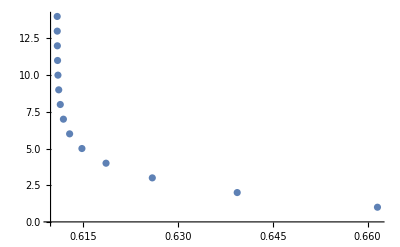

```mathematica
a1=0.45
a2=0.3
T = π÷4
rhobath={{1-a2,0},{0,a2}};
rho1initial = {{1-a1,0},{0,a1}};
For[i=1;n=1;rhostart = KroneckerProduct[rho1initial,rhobath],i<15,i++;n++,rhostart=KroneckerProduct[rho1initial,rhobath];rhostart=Ufor2.rhostart.Ufor2t;{rho1initial = TraceSystem[rhostart,{2}]//FullSimplify,Print[i],Ent[i_]:=Ent[i]= -Tr[rho1initial .MatrixLog[rho1initial]] //FullSimplify,Print[-Tr[rho1initial .MatrixLog[rho1initial]]],Print[Ent[i]]}]//FullSimplify 
ListPlot[Table[{Ent[i],i},{i,14}]]
```

Two qubits with random unitaries with no energy preservation condition. Bath qubit gets set to initial state after every interaction

0.45

0.3

1

0.667692+6.49878×10^-19 ⅈ

0.667692+6.49878×10^-19 ⅈ

2

0.671144+1.48569×10^-18 ⅈ

0.671144+1.48569×10^-18 ⅈ

3

0.665499+1.11536×10^-17 ⅈ

0.665499+1.11536×10^-17 ⅈ

4

0.660862+1.31114×10^-17 ⅈ

0.660862+1.31114×10^-17 ⅈ

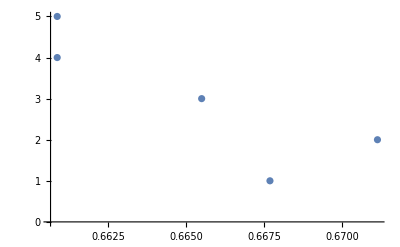

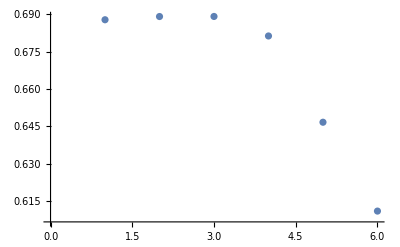

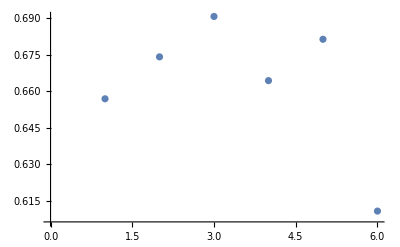

```mathematica
a1=0.45
a2=0.3
rhobath={{1-a2,0},{0,a2}};
rho1initial = {{1-a1,0},{0,a1}};
For[i=1;rhostart = KroneckerProduct[rho1initial,rhobath],i<5,i++, unitary = RU[4] ;transposeunitary = ConjugateTranspose[unitary];rhostart=KroneckerProduct[rho1initial,rhobath];rhostart=unitary.rhostart.transposeunitary;{rho1initial = TraceSystem[rhostart,{2}]//FullSimplify,Print[i],Ent2[i_]:=Ent2[i]= -Tr[rho1initial .MatrixLog[rho1initial]] //FullSimplify,Print[-Tr[rho1initial .MatrixLog[rho1initial]]],Print[Ent2[i]]}]//FullSimplify 
ListPlot[Table[{Re[Ent2[i]],i},{i,5}]]
Clear[Ent2]
ListPlot[{{1,0.6878600129198568},{2,0.6891581520942041},{3,0.6891844530883763},{4,0.6813332365545717},{5,0.646617713002646},{6,Enother}}]   
ListPlot[{{1,0.6569668652380932},{2,0.6741813392848317},{3,0.6907683006350249},{4,0.6644237472722745},{5,0.6814019514167171},{6,Enother}}]
```

Two qubits with random unitaries but with energy preservation (random angles of rotation)

```mathematica
a1=0.45;
a2=0.3;
rhobath={{1-a2,0},{0,a2}};
rho1initial = {{1-a1,0},{0,a1}};
Clear[T]
Unitfor2[y_] := Unitfor2[y] = {{1,0,0,0},{0,Cos[y*π],-Sin[y*π],0},{0,Sin[y*π],Cos[y*π],0},{0,0,0,1}}
Unitfor2t[y_]:= Unitfor2t[y] = Transpose[Unitfor2[y]]
```

1

0.703938

0.703938

2

0.567829

0.567829

3

0.563787

0.563787

4

0.42871

0.42871

5

0.427853

0.427853

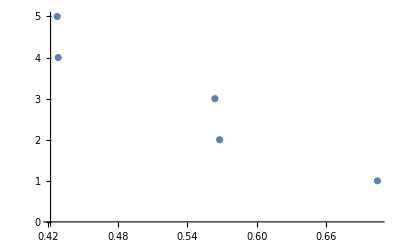

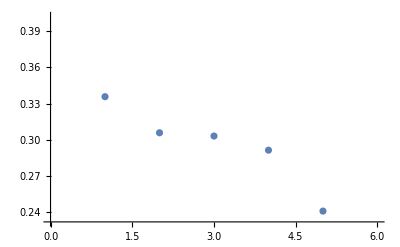

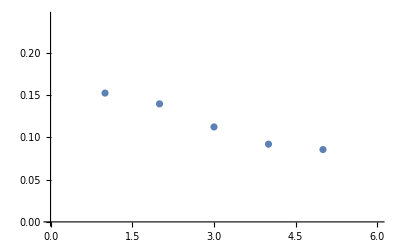

```mathematica
For[i=1;rhostart = KroneckerProduct[rho1initial,rhobath],i<6,i++,angle = RandomReal[{0,2}];rhostart=KroneckerProduct[rho1initial,rhobath];rhostart=Unitfor2[angle]*rhostart*Unitfor2t[angle];rho1initial = TraceSystem[rhostart,{2}]//FullSimplify;Print[i]; Ent3[i_]:=Ent3[i]= -Tr[rho1initial .MatrixLog[rho1initial]] //FullSimplify;Print[-Tr[rho1initial .MatrixLog[rho1initial]]];Print[Ent3[i]]]//FullSimplify 
ListPlot[Table[{Re[Ent3[i]],i},{i,5}]]
Clear[Ent3]

ListPlot[{{1,0.33572379286823795},{2,0.3058622058108845},{3,0.30315349366615396},{4,0.29145776345246177},{5,0.24104572522528778},{6,Enother}}]    
ListPlot[{{1,0.15261687315112119},{2,0.13984177010371304},{3,0.11251679719379185},{4,0.09209634022093631},{5,0.08571245726500398},{6,Enother}}]
```

```mathematica
DensityPlot[Eigfor2,{a1,0,0.5},{a2,0,0.5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,Automatic}]
```

-Graphics-

0.1

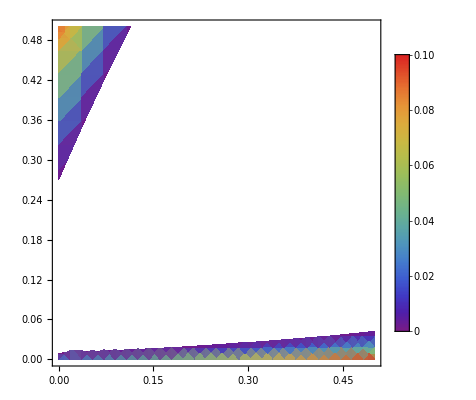

```mathematica
a3=0.1
DensityPlot[Eig13,{a1,0,0.5},{a2,0,0.5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,Automatic}]
```

```mathematica
Hfour = {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
MatrixForm[Hfour]
H4int = {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,ⅈ g,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-ⅈ g,0,0,ⅈ g,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,ⅈ g,0,0,0,0,0,0,0,0,0,0},{0,0,-ⅈ g,0,0,0,0,ⅈ g,0,0,0,0,0,0,0,0},{0,0,0,-ⅈ g,0,0,ⅈ g,0,ⅈ g,0,0,0,0,0,0,0},{0,0,0,0,0,-ⅈ g,0,0,0,0,ⅈ g,0,0,0,0,0},{0,0,0,0,-ⅈ g,0,0,0,0,0,0,ⅈ g,0,0,0,0},{0,0,0,0,0,-ⅈ g,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,ⅈ g,0,0,0,0,0},{0,0,0,0,0,0,-ⅈ g,0,0,-ⅈ g,0,0,ⅈ g,0,0,0},{0,0,0,0,0,0,0,-ⅈ g,0,0,0,0,0,ⅈ g,0,0},{0,0,0,0,0,0,0,0,0,0,-ⅈ g,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-ⅈ g,0,0,ⅈ g,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-ⅈ g,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
MatrixForm[H4int]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0 | ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
a1=0.14
a2=0.16
a3=0.3
```

0.14

0.16

0.3

```mathematica
t=π/(2(2)^0.5)
```

1.11072

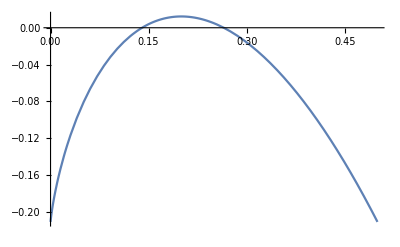

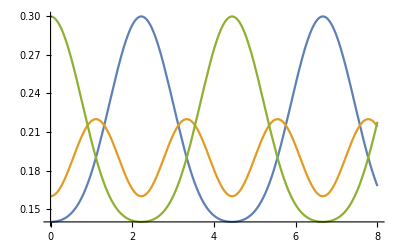

-0.00471384

{{a→0.264923}}

```mathematica
RelEnt[rho_ , sigma_] := Tr[{{1-rho,0},{0,rho}}.MatrixLog[{{1-rho,0},{0,rho}}]-{{1-rho,0},{0,rho}}.MatrixLog[{{1-sigma,0},{0,sigma}}]]
Plot[RelEnt[0.14,0.2]-RelEnt[a,0.2],{a,0,0.5}]
Plot[{rho1[[2,2]],rho2[[2,2]],rho3[[2,2]]},{t,0,8}]
RelEnt[0.14,0.2]-RelEnt[0.13,0.2]
FindInstance[RelEnt[0.14,0.2]-RelEnt[a,0.2]==0,a,Reals]
```

```mathematica
Plot[{RelEnt[0.14,0.2]-RelEnt[rho1[[2,2]],0.2],RelEnt[0.16,0.2]-RelEnt[rho2[[2,2]],0.2],RelEnt[0.3,0.2]-RelEnt[rho3[[2,2]],0.2]},{t,0,8}];
Plot[{S1,S2,S3,-Tr[{{1-0.2,0},{0,0.2}}MatrixLog[{{1-0.2,0},{0,0.2}}]],RelEnt[0.14,0.2]-RelEnt[rho1[[2,2]],0.2]},{t,0,8}];
Plot[{RelEnt[0.14,0.2]-RelEnt[rho1[[2,2]],0.2],RelEnt[0.3,0.2]-RelEnt[rho1[[2,2]],0.2],{RelEnt[0.16,0.2]-RelEnt[rho1[[2,2]],0.2]}},{t,0,8}];
```

0.15

0.22

0.5

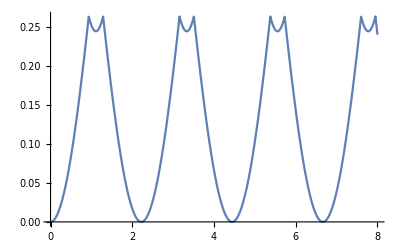

```mathematica
a1=0.15
a2=0.22
a3=0.5
Plot[{-Abs[rho2[[2,2]]-rho1[[2,2]]]-Abs[rho3[[2,2]]-rho2[[2,2]]]+(a3-a1)},{t,0,8}]
```

```mathematica
Clear[a1,a2,a3,t]
rho1
```

{{1/8 (8-3 a1-2 a2-3 a3+4 (-a1+a3) Cos[√2 t]-(a1-2 a2+a3) Cos[2 √2 t]),0},{0,1/8 (3 a1+2 a2+3 a3+4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) Cos[2 √2 t])}}

```mathematica
a1=0.03
a2=0.3
Plot3D[-Abs[rho2[[2,2]]-rho1[[2,2]]]-Abs[rho3[[2,2]]-rho2[[2,2]]]+(a3-a1),{a3,0.3,0.5},{t,0,0.8}]//FullSimplify
```

0.03

0.3

-Graphics3D-

```mathematica
Clear[a1,a2,a3,t]
-Abs[rho2[[2,2]]-rho1[[2,2]]]-Abs[rho3[[2,2]]-rho2[[2,2]]]-Abs[rho3[[2,2]]-rho1[[2,2]]]+2(a3-a1)//FullSimplify
```

-2 a1+2 a3-Abs[(-a1+a3) Cos[√2 t]]-1/8 Abs[4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t])]-1/8 Abs[4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t])]

```mathematica
Manipulate[Plot[-2 a1+2 a3-Abs[(-a1+a3) Cos[√2 t]]-1/8 Abs[4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t])]-1/8 Abs[4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t])],{t,-2.221441469079183,2.2214414690791826}],{a1,-3.13523138347365,3.13523138347365},{a2,-2,2},{a3,-2,2}]
```

```mathematica
Manipulate[Plot[{Abs[rho2[[2,2]]-rho1[[2,2]]],Abs[rho3[[2,2]]-rho2[[2,2]]]},{t,-2.221441469079183,2.2214414690791826}],{a1,-3.729822128134704,3.729822128134704},{a2,-2,2},{a3,-2,2}]
```

```mathematica
Manipulate[Plot[-a1+a3-1/8 Abs[4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t])]-1/8 Abs[4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t])],{t,-2.221441469079183,2.2214414690791826}],{a1,-3.729822128134704,3.729822128134704},{a2,-2,2},{a3,-2,2}]
```

```mathematica
e3
```

e3

```mathematica
-((rho2[[2,2]]-rho1[[2,2]])^2)^0.5-((rho3[[2,2]]-rho2[[2,2]])^2)^0.5+(a3-a1)//FullSimplify
```

0.1

```mathematica
TrigReduce[-a1+a3-0.125 ((4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t]))^2)^0.5-0.125 ((4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t]))^2)^0.5]
```

0.1

```mathematica
Manipulate[Plot[-0.125 (8. a1-8. a3+1. ((4 (a1-a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t]))^2)^0.5+1. ((4 (-a1+a3) Cos[√2 t]+(a1-2 a2+a3) (1+3 Cos[2 √2 t]))^2)^0.5),{t,-2.221441469079183,2.2214414690791826}],{a1,-6.8175375331502295,6.8175375331502295},{a2,-2,2},{a3,-2,2}]
```

```mathematica
Hfor4 = {{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,ⅈ,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-ⅈ,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
Ufor4 = MatrixExp[Hfor4 I θ ];
rhofor4[a1_,a2_,a3_,a4_] := KroneckerProduct[{{1-a1,0},{0,a1}},{{1-a2,0},{0,a2}},{{1-a3,0},{0,a3}},{{1-a4,0},{0,a4}}]
rhofor4t = Ufor4. rhofor4[a1,a2,a3,a4].Transpose[Ufor4]//FullSimplify;
Clear[rho1, rho2, rho3,rho1in, rho2in, rho3in,a1,a2,a3,a4]
rho1 = TraceSystem[rhofor4t ,{2,3,4}];
rho2 = TraceSystem[rhofor4t ,{1,3,4}];
rho3 = TraceSystem[rhofor4t ,{1,2,4}];
rho4 = TraceSystem[rhofor4t ,{1,2,3}];
rho1in = TraceSystem[rhofor4t ,{2,3,4}];
rho2in = TraceSystem[rhofor4t ,{1,3,4}];
rho3in = TraceSystem[rhofor4t ,{1,2,4}];
rho4in = TraceSystem[rhofor4t ,{1,2,3}];
```

```mathematica
rho14 = TraceSystem[rhofor4t ,{2,3}]
rho12 = TraceSystem[rhofor4t ,{3,4}];
rho13 = TraceSystem[rhofor4t ,{2,4}];
```

{{(-1+a1) (-1+a2) (-a1-a2-a3) (-1+a3)-(-1+a1) a2 (-a1-a2-a3) (-1+a3)-(-1+a1) (-1+a2) (-a1-a2-a3) a3+(-1+a1) a2 (-a1-a2-a3) a3 Cos[θ]^2+a1 (-1+a2) (1-a1-a2-a3) (-1+a3) Sin[θ]^2,0,0,0},{0,-(-1+a1) (-1+a2) (1-a1-a2-a3) (-1+a3)-(-1+a1) a2 (1-a1-a2-a3) a3+(-1+a1) a2 (1-a1-a2-a3) (-1+a3) Cos[θ]^2+(-1+a1) (-1+a2) (1-a1-a2-a3) a3 Cos[θ]^2+a1 a2 (-a1-a2-a3) (-1+a3) Sin[θ]^2+a1 (-1+a2) (-a1-a2-a3) a3 Sin[θ]^2,0,0},{0,0,-a1 (-1+a2) (-a1-a2-a3) (-1+a3)-a1 a2 (-a1-a2-a3) a3+a1 a2 (-a1-a2-a3) (-1+a3) Cos[θ]^2+a1 (-1+a2) (-a1-a2-a3) a3 Cos[θ]^2+(-1+a1) a2 (1-a1-a2-a3) (-1+a3) Sin[θ]^2+(-1+a1) (-1+a2) (1-a1-a2-a3) a3 Sin[θ]^2,0},{0,0,0,-a1 a2 (1-a1-a2-a3) (-1+a3)-a1 (-1+a2) (1-a1-a2-a3) a3+a1 a2 (1-a1-a2-a3) a3+a1 (-1+a2) (1-a1-a2-a3) (-1+a3) Cos[θ]^2+(-1+a1) a2 (-a1-a2-a3) a3 Sin[θ]^2}}

```mathematica
MatrixForm[rho14]
```

rho14

```mathematica
a1=0.01
a2=0.26
a3=0.3
a4=0.4
```

0.01

0.26

0.3

0.4

0.01

0.26

0.3

0.4

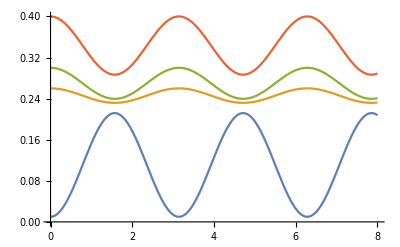

```mathematica
Plot[{rho1in[[2,2]],rho2[[2,2]],rho3[[2,2]],rho4[[2,2]]rho1[[2,2]],rho2[[2,2]],rho3[[2,2]],rho4[[2,2]]},{θ,0,8}]
```

```mathematica
Abs[rho1in[[2,2]]-rho2in[[2,2]]]+Abs[rho2in[[2,2]]-rho3in[[2,2]]]+Abs[rho3in[[2,2]]-rho4in[[2,2]]] - Abs[rho1[[2,2]]-rho2[[2,2]]]+Abs[rho2[[2,2]]-rho3[[2,2]]]+Abs[rho3[[2,2]]-rho4[[2,2]]]
```

```mathematica
2 Abs[-(-1+a1) (-1+a2) a3 (-1+a4)-a1 a2 a3 (-1+a4)+(-1+a1) (-1+a2) (-1+a3) a4+a1 a2 (-1+a3) a4+a1 (-1+a2) a3 (-1+a4) Cos[θ]^2+(-1+a1) a2 a3 (-1+a4) Cos[θ]^2-a1 (-1+a2) (-1+a3) a4 Cos[θ]^2-(-1+a1) a2 (-1+a3) a4 Cos[θ]^2-a1 (-1+a2) a3 (-1+a4) Sin[θ]^2-(-1+a1) a2 a3 (-1+a4) Sin[θ]^2+a1 (-1+a2) (-1+a3) a4 Sin[θ]^2+(-1+a1) a2 (-1+a3) a4 Sin[θ]^2]+2 Abs[-(-1+a1) a2 (-1+a3) (-1+a4)+(-1+a1) (-1+a2) a3 (-1+a4)-a1 a2 (-1+a3) a4+a1 (-1+a2) a3 a4+a1 a2 (-1+a3) (-1+a4) Cos[θ]^2-a1 (-1+a2) a3 (-1+a4) Cos[θ]^2+(-1+a1) a2 (-1+a3) a4 Cos[θ]^2-(-1+a1) (-1+a2) a3 a4 Cos[θ]^2-a1 a2 (-1+a3) (-1+a4) Sin[θ]^2+a1 (-1+a2) a3 (-1+a4) Sin[θ]^2-(-1+a1) a2 (-1+a3) a4 Sin[θ]^2+(-1+a1) (-1+a2) a3 a4 Sin[θ]^2]
```

2 Abs[(1-a1) (-1+a2) a3 (-1+a4)-a1 a2 a3 (-1+a4)+(-1+a1) (-1+a2) (-1+a3) a4+a1 a2 (-1+a3) a4+a1 (-1+a2) a3 (-1+a4) Cos[θ]^2+(-1+a1) a2 a3 (-1+a4) Cos[θ]^2-a1 (-1+a2) (-1+a3) a4 Cos[θ]^2-(-1+a1) a2 (-1+a3) a4 Cos[θ]^2-a1 (-1+a2) a3 (-1+a4) Sin[θ]^2-(-1+a1) a2 a3 (-1+a4) Sin[θ]^2+a1 (-1+a2) (-1+a3) a4 Sin[θ]^2+(-1+a1) a2 (-1+a3) a4 Sin[θ]^2]+2 Abs[(1-a1) a2 (-1+a3) (-1+a4)+(-1+a1) (-1+a2) a3 (-1+a4)-a1 a2 (-1+a3) a4+a1 (-1+a2) a3 a4+a1 a2 (-1+a3) (-1+a4) Cos[θ]^2-a1 (-1+a2) a3 (-1+a4) Cos[θ]^2+(-1+a1) a2 (-1+a3) a4 Cos[θ]^2-(-1+a1) (-1+a2) a3 a4 Cos[θ]^2-a1 a2 (-1+a3) (-1+a4) Sin[θ]^2+a1 (-1+a2) a3 (-1+a4) Sin[θ]^2-(-1+a1) a2 (-1+a3) a4 Sin[θ]^2+(-1+a1) (-1+a2) a3 a4 Sin[θ]^2]

```mathematica
Manipulate[Plot[%701,{θ,0,2 π}],{a1,-5.,5.},{a2,-5.,5.},{a3,-2,2},{a4,-2,2}]
```

```mathematica
Simplify[%698]
```

%698

```mathematica
Manipulate[Plot[%696,{θ,0,2 π}],{a1,-5.,5.},{a2,-5.,5.},{a3,-2,2},{a4,-2,2}]
```

```mathematica
Eig13 = Abs[rho13[[2,3]]]-(rho13[[1,1]]*rho13[[4,4]])^0.5
a4=1-a1-a2-a3
```

-((-a1 a2 (-a1-a2-a3) a3-a1 (-1+a2) (1-a1-a2-a3) a3+a1 a2 (1-a1-a2-a3) a3+a1 (-1+a2) (-a1-a2-a3) a3 Cos[θ]^2+(-1+a1) a2 (1-a1-a2-a3) (-1+a3) Sin[θ]^2) ((-1+a1) (-1+a2) (-a1-a2-a3) (-1+a3)-(-1+a1) a2 (-a1-a2-a3) (-1+a3)-(-1+a1) (-1+a2) (1-a1-a2-a3) (-1+a3)+(-1+a1) a2 (1-a1-a2-a3) (-1+a3) Cos[θ]^2+a1 (-1+a2) (-a1-a2-a3) a3 Sin[θ]^2))^0.5

1-a1-a2-a3

```mathematica
DensityPlot3D[Eig12,{a1,0,0.5},{a2,0,0.5},{a3,0,0.5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,Automatic}]
```

-Graphics3D-

```mathematica
Eig12 = Abs[rho12[[2,3]]]-(rho12[[1,1]]*rho12[[4,4]])^0.5;
Eig14 = Abs[rho23[[2,3]]]-(rho23[[1,1]]*rho23[[4,4]])^0.5;
```

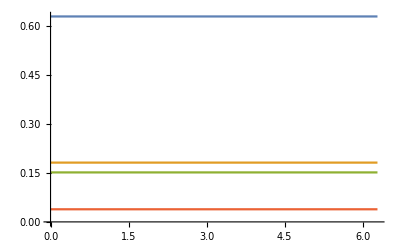

```mathematica
Plot[{rho12[[1,1]],rho12[[2,2]],rho12[[3,3]],rho12[[4,4]]},{θ,0,2 π}]
```

```mathematica
c\0cde3\
```